## Definitions

```mathematica
Get["/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/DTQW.wl"]
```

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

## Initializations

```mathematica
InitializeDTQW[2,201]
```

```mathematica
coin=MakeCoin[1/2,0,0]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
shift=MakeShift[];
```

```mathematica
MakeUnitary[];
```

## Procedure

```mathematica
psi0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{ⅈ/(√2),1,0}}]

```mathematica
DTQW2[psi0,100]
```

{{0.+0. ⅈ},{0.+0. ⅈ},{6.28037×10^-16-6.28037×10^-16 ⅈ},{0.+0. ⅈ},{5.96635×10^-14-6.09196×10^-14 ⅈ},{0.+0. ⅈ},{2.68486×10^-12-2.80293×10^-12 ⅈ},{0.+0. ⅈ},{7.60685×10^-11-8.13226×10^-11 ⅈ},{0.+0. ⅈ},{1.52114×10^-9-1.66825×10^-9 ⅈ},{0.+0. ⅈ},{2.28073×10^-8-2.57123×10^-8 ⅈ},{0.+0. ⅈ},{2.6582×10^-7-3.08795×10^-7 ⅈ},{0.+0. ⅈ},{2.46329×10^-6-2.95699×10^-6 ⅈ},{0.+0. ⅈ},{0.0000184034-0.0000229076 ⅈ},{0.+0. ⅈ},{0.000111683-0.000144768 ⅈ},{0.+0. ⅈ},{0.000551635-0.000748696 ⅈ},{0.+0. ⅈ},{0.00220963-0.0031629 ⅈ},{0.+0. ⅈ},{0.00710242-0.0108314 ⅈ},{0.+0. ⅈ},{0.0179386-0.0295977 ⅈ},{0.+0. ⅈ},{0.0341883-0.0626581 ⅈ},{0.+0. ⅈ},{0.0449906-0.0968872 ⅈ},{0.+0. ⅈ},{0.0306075-0.094323 ⅈ},{0.+0. ⅈ},{-0.0115551-0.0245063 ⅈ},{0.+0. ⅈ},{-0.0393175+0.065591 ⅈ},{0.+0. ⅈ},{-0.00800604+0.0627082 ⅈ},{0.+0. ⅈ},{0.0370025-0.0386901 ⅈ},{0.+0. ⅈ},{0.0089323-0.0635073 ⅈ},{0.+0. ⅈ},{-0.0381701+0.0407706 ⅈ},{0.+0. ⅈ},{0.00460853+0.0488463 ⅈ},{0.+0. ⅈ},{0.0353354-0.0588314 ⅈ},{0.+0. ⅈ},{-0.0279733-0.0118394 ⅈ},{0.+0. ⅈ},{-0.0125157+0.0634824 ⅈ},{0.+0. ⅈ},{0.0390391-0.0421593 ⅈ},{0.+0. ⅈ},{-0.0279682-0.0191879 ⅈ},{0.+0. ⅈ},{-0.00659563+0.0596935 ⅈ},{0.+0. ⅈ},{0.0354604-0.0508993 ⅈ},{0.+0. ⅈ},{-0.0400256+0.00743173 ⅈ},{0.+0. ⅈ},{0.0209827+0.0375971 ⅈ},{0.+0. ⅈ},{0.00830717-0.0592157 ⅈ},{0.+0. ⅈ},{-0.0329475+0.0513971 ⅈ},{0.+0. ⅈ},{0.043955-0.0231565 ⅈ},{0.+0. ⅈ},{-0.0399253-0.0110308 ⅈ},{0.+0. ⅈ},{0.0248086+0.0390864 ⅈ},{0.+0. ⅈ},{-0.00456997-0.0547549 ⅈ},{0.+0. ⅈ},{-0.0154204+0.0573329 ⅈ},{0.+0. ⅈ},{0.0316619-0.0496227 ⅈ},{0.+0. ⅈ},{-0.0426782+0.0357223 ⅈ},{0.+0. ⅈ},{0.048549-0.019464 ⅈ},{0.+0. ⅈ},{-0.050265+0.00365734 ⅈ},{0.+0. ⅈ},{0.0491686+0.0100513 ⅈ},{0.+0. ⅈ},{-0.0465829-0.0209776 ⅈ},{0.+0. ⅈ},{0.0436212+0.029079 ⅈ},{0.+0. ⅈ},{-0.0411285-0.0346477 ⅈ},{0.+0. ⅈ},{0.0396953+0.0380751 ⅈ},{0.+0. ⅈ},{-0.0396953-0.0396953 ⅈ},{0.+0. ⅈ},{0.0413155+0.0396953 ⅈ},{0.+0. ⅈ},{-0.0445559-0.0380751 ⅈ},{0.+0. ⅈ},{0.0491898+0.0346477 ⅈ},{0.+0. ⅈ},{-0.0546842-0.029079 ⅈ},{0.+0. ⅈ},{0.060095+0.0209776 ⅈ},{0.+0. ⅈ},{-0.0639736-0.0100513 ⅈ},{0.+0. ⅈ},{0.0643556-0.00365734 ⅈ},{0.+0. ⅈ},{-0.0589365+0.019464 ⅈ},{0.+0. ⅈ},{0.0455623-0.0357223 ⅈ},{0.+0. ⅈ},{-0.0231306+0.0496227 ⅈ},{0.+0. ⅈ},{-0.00714791-0.0573329 ⅈ},{0.+0. ⅈ},{0.0404772+0.0547549 ⅈ},{0.+0. ⅈ},{-0.0679808-0.0390864 ⅈ},{0.+0. ⅈ},{0.0781423+0.0110308 ⅈ},{0.+0. ⅈ},{-0.0611881+0.0231565 ⅈ},{0.+0. ⅈ},{0.0161257-0.0513971 ⅈ},{0.+0. ⅈ},{0.0426013+0.0592157 ⅈ},{0.+0. ⅈ},{-0.0850544-0.0375971 ⅈ},{0.+0. ⅈ},{0.078928-0.00743173 ⅈ},{0.+0. ⅈ},{-0.0153898+0.0508993 ⅈ},{0.+0. ⅈ},{-0.0684737-0.0596935 ⅈ},{0.+0. ⅈ},{0.100386+0.0191879 ⅈ},{0.+0. ⅈ},{-0.0338388+0.0421593 ⅈ},{0.+0. ⅈ},{-0.0796164-0.0634824 ⅈ},{0.+0. ⅈ},{0.106006+0.0118394 ⅈ},{0.+0. ⅈ},{0.0145937+0.0588314 ⅈ},{0.+0. ⅈ},{-0.127787-0.0488463 ⅈ},{0.+0. ⅈ},{0.0316691-0.0407706 ⅈ},{0.+0. ⅈ},{0.1392+0.0635073 ⅈ},{0.+0. ⅈ},{-0.0320242+0.0386901 ⅈ},{0.+0. ⅈ},{-0.167617-0.0627082 ⅈ},{0.+0. ⅈ},{-0.0526398-0.065591 ⅈ},{0.+0. ⅈ},{0.149437+0.0245063 ⅈ},{0.+0. ⅈ},{0.236201+0.094323 ⅈ},{0.+0. ⅈ},{0.193734+0.0968872 ⅈ},{0.+0. ⅈ},{0.110194+0.0626581 ⅈ},{0.+0. ⅈ},{0.0475316+0.0295977 ⅈ},{0.+0. ⅈ},{0.016204+0.0108314 ⅈ},{0.+0. ⅈ},{0.00446323+0.0031629 ⅈ},{0.+0. ⅈ},{0.00100515+0.000748696 ⅈ},{0.+0. ⅈ},{0.000186079+0.000144768 ⅈ},{0.+0. ⅈ},{0.0000283279+0.0000229076 ⅈ},{0.+0. ⅈ},{3.53161×10^-6+2.95699×10^-6 ⅈ},{0.+0. ⅈ},{3.57314×10^-7+3.08795×10^-7 ⅈ},{0.+0. ⅈ},{2.89017×10^-8+2.57123×10^-8 ⅈ},{0.+0. ⅈ},{1.82564×10^-9+1.66825×10^-9 ⅈ},{0.+0. ⅈ},{8.68104×10^-11+8.13226×10^-11 ⅈ},{0.+0. ⅈ},{2.92351×10^-12+2.80293×10^-12 ⅈ},{0.+0. ⅈ},{6.21757×10^-14+6.09196×10^-14 ⅈ},{0.+0. ⅈ},{6.28037×10^-16+6.28037×10^-16 ⅈ},{-6.28037×10^-16+6.28037×10^-16 ⅈ},{0.+0. ⅈ},{-6.09196×10^-14+6.21757×10^-14 ⅈ},{0.+0. ⅈ},{-2.80293×10^-12+2.92351×10^-12 ⅈ},{0.+0. ⅈ},{-8.13226×10^-11+8.68104×10^-11 ⅈ},{0.+0. ⅈ},{-1.66825×10^-9+1.82564×10^-9 ⅈ},{0.+0. ⅈ},{-2.57123×10^-8+2.89017×10^-8 ⅈ},{0.+0. ⅈ},{-3.08795×10^-7+3.57314×10^-7 ⅈ},{0.+0. ⅈ},{-2.95699×10^-6+3.53161×10^-6 ⅈ},{0.+0. ⅈ},{-0.0000229076+0.0000283279 ⅈ},{0.+0. ⅈ},{-0.000144768+0.000186079 ⅈ},{0.+0. ⅈ},{-0.000748696+0.00100515 ⅈ},{0.+0. ⅈ},{-0.0031629+0.00446323 ⅈ},{0.+0. ⅈ},{-0.0108314+0.016204 ⅈ},{0.+0. ⅈ},{-0.0295977+0.0475316 ⅈ},{0.+0. ⅈ},{-0.0626581+0.110194 ⅈ},{0.+0. ⅈ},{-0.0968872+0.193734 ⅈ},{0.+0. ⅈ},{-0.094323+0.236201 ⅈ},{0.+0. ⅈ},{-0.0245063+0.149437 ⅈ},{0.+0. ⅈ},{0.065591-0.0526398 ⅈ},{0.+0. ⅈ},{0.0627082-0.167617 ⅈ},{0.+0. ⅈ},{-0.0386901-0.0320242 ⅈ},{0.+0. ⅈ},{-0.0635073+0.1392 ⅈ},{0.+0. ⅈ},{0.0407706+0.0316691 ⅈ},{0.+0. ⅈ},{0.0488463-0.127787 ⅈ},{0.+0. ⅈ},{-0.0588314+0.0145937 ⅈ},{0.+0. ⅈ},{-0.0118394+0.106006 ⅈ},{0.+0. ⅈ},{0.0634824-0.0796164 ⅈ},{0.+0. ⅈ},{-0.0421593-0.0338388 ⅈ},{0.+0. ⅈ},{-0.0191879+0.100386 ⅈ},{0.+0. ⅈ},{0.0596935-0.0684737 ⅈ},{0.+0. ⅈ},{-0.0508993-0.0153898 ⅈ},{0.+0. ⅈ},{0.00743173+0.078928 ⅈ},{0.+0. ⅈ},{0.0375971-0.0850544 ⅈ},{0.+0. ⅈ},{-0.0592157+0.0426013 ⅈ},{0.+0. ⅈ},{0.0513971+0.0161257 ⅈ},{0.+0. ⅈ},{-0.0231565-0.0611881 ⅈ},{0.+0. ⅈ},{-0.0110308+0.0781423 ⅈ},{0.+0. ⅈ},{0.0390864-0.0679808 ⅈ},{0.+0. ⅈ},{-0.0547549+0.0404772 ⅈ},{0.+0. ⅈ},{0.0573329-0.00714791 ⅈ},{0.+0. ⅈ},{-0.0496227-0.0231306 ⅈ},{0.+0. ⅈ},{0.0357223+0.0455623 ⅈ},{0.+0. ⅈ},{-0.019464-0.0589365 ⅈ},{0.+0. ⅈ},{0.00365734+0.0643556 ⅈ},{0.+0. ⅈ},{0.0100513-0.0639736 ⅈ},{0.+0. ⅈ},{-0.0209776+0.060095 ⅈ},{0.+0. ⅈ},{0.029079-0.0546842 ⅈ},{0.+0. ⅈ},{-0.0346477+0.0491898 ⅈ},{0.+0. ⅈ},{0.0380751-0.0445559 ⅈ},{0.+0. ⅈ},{-0.0396953+0.0413155 ⅈ},{0.+0. ⅈ},{0.0396953-0.0396953 ⅈ},{0.+0. ⅈ},{-0.0380751+0.0396953 ⅈ},{0.+0. ⅈ},{0.0346477-0.0411285 ⅈ},{0.+0. ⅈ},{-0.029079+0.0436212 ⅈ},{0.+0. ⅈ},{0.0209776-0.0465829 ⅈ},{0.+0. ⅈ},{-0.0100513+0.0491686 ⅈ},{0.+0. ⅈ},{-0.00365734-0.050265 ⅈ},{0.+0. ⅈ},{0.019464+0.048549 ⅈ},{0.+0. ⅈ},{-0.0357223-0.0426782 ⅈ},{0.+0. ⅈ},{0.0496227+0.0316619 ⅈ},{0.+0. ⅈ},{-0.0573329-0.0154204 ⅈ},{0.+0. ⅈ},{0.0547549-0.00456997 ⅈ},{0.+0. ⅈ},{-0.0390864+0.0248086 ⅈ},{0.+0. ⅈ},{0.0110308-0.0399253 ⅈ},{0.+0. ⅈ},{0.0231565+0.043955 ⅈ},{0.+0. ⅈ},{-0.0513971-0.0329475 ⅈ},{0.+0. ⅈ},{0.0592157+0.00830717 ⅈ},{0.+0. ⅈ},{-0.0375971+0.0209827 ⅈ},{0.+0. ⅈ},{-0.00743173-0.0400256 ⅈ},{0.+0. ⅈ},{0.0508993+0.0354604 ⅈ},{0.+0. ⅈ},{-0.0596935-0.00659563 ⅈ},{0.+0. ⅈ},{0.0191879-0.0279682 ⅈ},{0.+0. ⅈ},{0.0421593+0.0390391 ⅈ},{0.+0. ⅈ},{-0.0634824-0.0125157 ⅈ},{0.+0. ⅈ},{0.0118394-0.0279733 ⅈ},{0.+0. ⅈ},{0.0588314+0.0353354 ⅈ},{0.+0. ⅈ},{-0.0488463+0.00460853 ⅈ},{0.+0. ⅈ},{-0.0407706-0.0381701 ⅈ},{0.+0. ⅈ},{0.0635073+0.0089323 ⅈ},{0.+0. ⅈ},{0.0386901+0.0370025 ⅈ},{0.+0. ⅈ},{-0.0627082-0.00800604 ⅈ},{0.+0. ⅈ},{-0.065591-0.0393175 ⅈ},{0.+0. ⅈ},{0.0245063-0.0115551 ⅈ},{0.+0. ⅈ},{0.094323+0.0306075 ⅈ},{0.+0. ⅈ},{0.0968872+0.0449906 ⅈ},{0.+0. ⅈ},{0.0626581+0.0341883 ⅈ},{0.+0. ⅈ},{0.0295977+0.0179386 ⅈ},{0.+0. ⅈ},{0.0108314+0.00710242 ⅈ},{0.+0. ⅈ},{0.0031629+0.00220963 ⅈ},{0.+0. ⅈ},{0.000748696+0.000551635 ⅈ},{0.+0. ⅈ},{0.000144768+0.000111683 ⅈ},{0.+0. ⅈ},{0.0000229076+0.0000184034 ⅈ},{0.+0. ⅈ},{2.95699×10^-6+2.46329×10^-6 ⅈ},{0.+0. ⅈ},{3.08795×10^-7+2.6582×10^-7 ⅈ},{0.+0. ⅈ},{2.57123×10^-8+2.28073×10^-8 ⅈ},{0.+0. ⅈ},{1.66825×10^-9+1.52114×10^-9 ⅈ},{0.+0. ⅈ},{8.13226×10^-11+7.60685×10^-11 ⅈ},{0.+0. ⅈ},{2.80293×10^-12+2.68486×10^-12 ⅈ},{0.+0. ⅈ},{6.09196×10^-14+5.96635×10^-14 ⅈ},{0.+0. ⅈ},{6.28037×10^-16+6.28037×10^-16 ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
posρ=MatrixPartialTrace[%12.%12†,1,{2,201}]
```

```mathematica
probs=Abs[Diagonal[posρ]]
```

{7.88861×10^-31,0.,7.5778×10^-27,0.,1.64106×10^-23,0.,1.41645×10^-20,0.,6.12844×10^-18,0.,1.50153×10^-15,0.,2.24209×10^-13,0.,2.13821×10^-11,0.,1.34204×10^-9,0.,5.64463×10^-8,0.,1.6043×10^-6,0.,0.0000307892,0.,0.000394775,0.,0.00330304,0.,0.0172667,0.,0.0520147,0.,0.076099,0.,0.0327656,0.,0.0078072,0.,0.0378757,0.,0.00651889,0.,0.0262759,0.,0.00677814,0.,0.0218347,0.,0.00608131,0.,0.0160872,0.,0.0112915,0.,0.00710913,0.,0.0137471,0.,0.00940236,0.,0.0064344,0.,0.010133,0.,0.0103051,0.,0.00717518,0.,0.00647721,0.,0.00800741,0.,0.00869616,0.,0.00786484,0.,0.00677971,0.,0.00635714,0.,0.00652228,0.,0.00681689,0.,0.00694987,0.,0.00689088,0.,0.00673359,0.,0.00657005,0.,0.00644598,0.,0.0063685,0.,0.00632696,0.,0.00630811,0.,0.00630286,0.,0.00630811,0.,0.00632696,0.,0.0063685,0.,0.00644598,0.,0.00657005,0.,0.00673359,0.,0.00689088,0.,0.00694987,0.,0.00681689,0.,0.00652228,0.,0.00635714,0.,0.00677971,0.,0.00786484,0.,0.00869616,0.,0.00800741,0.,0.00647721,0.,0.00717518,0.,0.0103051,0.,0.010133,0.,0.0064344,0.,0.00940236,0.,0.0137471,0.,0.00710913,0.,0.0112915,0.,0.0160872,0.,0.00608131,0.,0.0218347,0.,0.00677814,0.,0.0262759,0.,0.00651889,0.,0.0378757,0.,0.0078072,0.,0.0327656,0.,0.076099,0.,0.0520147,0.,0.0172667,0.,0.00330304,0.,0.000394775,0.,0.0000307892,0.,1.6043×10^-6,0.,5.64463×10^-8,0.,1.34204×10^-9,0.,2.13821×10^-11,0.,2.24209×10^-13,0.,1.50153×10^-15,0.,6.12844×10^-18,0.,1.41645×10^-20,0.,1.64106×10^-23,0.,7.5778×10^-27,0.,7.88861×10^-31}

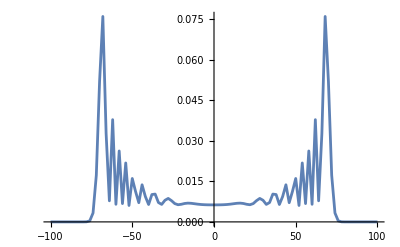

```mathematica
ListLinePlot[{Range[-100,100,2],probs[[;;;;2]]}ᵀ,
PlotRange->All
]
```

```mathematica
psi=DTQW2wDecoherence[psi0,0.5,100];
```

```mathematica
posRho=MatrixPartialTrace[psi,1,{2,201}];
```

```mathematica
probswD=Abs[Diagonal[posRho]];
```

```mathematica
probswD//Total
```

1.

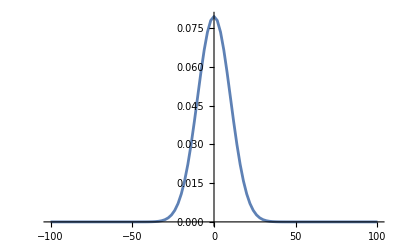

```mathematica
ListLinePlot[{Range[-100,100,2],probswD[[;;;;2]]}ᵀ,
PlotRange->All
]
```

```mathematica
randomWalk=Riffle[Binomial[100,#]/2^100&/@Range[0,100],0];
```

```mathematica
ListLinePlot[{Range[-100,100,2],randomWalk[[;;;;2]]}ᵀ,
PlotRange->All
]
```

-Graphics-

```mathematica
Round[probswD,5]==Round[randomWalk,5]
```

True